```mathematica
n1 = RandomInteger[{10^60,10^75}];
While[!PrimeQ[n1],n1 = n1 + 1];n1
n2 = RandomInteger[{10^60,10^75}];
While[!PrimeQ[n2],n2 = n2 + 1];n2
n = n1*n2
```

23582590110955324388077840713030107486409747967709379698042842323362725927

469430195916593256773061501011815865673870038881283632349318087566931230033

11070379896006472636728371001422666331204261780826494316719497957468523744110641556569681769497312551480998171999460706489696413040443391617970165591

```mathematica
d=5;min = ∞;
Table[m=Floor[(r n)^(1/d)];c=IntegerDigits[r n,m];t=∑_(i=1)^(d+1) c[[i]];If[t<min,mr=r;min=t,0],{r,10^4}];
```

```mathematica
mr
```

1302

```mathematica
m=Floor[(mr n)^(1/d)];c=IntegerDigits[mr n,m]
```

{1,4,89293879743580436844158763089,18589981291185238190405195370,121889004455969511048629002554,163774177654670505223386864360}

```mathematica
f[x_]:=c[[1]] x^5+c[[2]] x^4+c[[3]] x^3+c[[4]] x^2+c[[5]]x+c[[6]]
```

```mathematica
N[Solve[c[[1]] x^5+c[[2]] x^4+c[[3]] x^3+c[[4]] x^2+c[[5]]x+c[[6]]==0,x]]
```

{{x→-0.913092},{x→-1.89591-2.98821×10^14 ⅈ},{x→-1.89591+2.98821×10^14 ⅈ},{x→0.352452-1.37275 ⅈ},{x→0.352452+1.37275 ⅈ}}

```mathematica
Factor[c[[1]] x^5+c[[2]] x^4+c[[3]] x^3+c[[4]] x^2+c[[5]]x+c[[6]]]
```

163774177654670505223386864360+121889004455969511048629002554 x+18589981291185238190405195370 x^2+89293879743580436844158763089 x^3+4 x^4+x^5

```mathematica
c
```

{1,4,89293879743580436844158763089,18589981291185238190405195370,121889004455969511048629002554,163774177654670505223386864360}

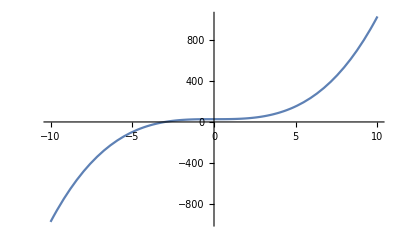

```mathematica
Plot[x^3+27,{x,-10,10}]
```

```mathematica
Solve[x^3+11^3/13^3==0,x]
```

{{x→-11/13},{x→11/13 (-1)^(1/3)},{x→-11/13 (-1)^(2/3)}}

```mathematica
Factor[(x-1)(x-1/2)(x-2^(1/2^(1/2)))]
```

1/2 (-1+x) (-2^(1/(√2))+x) (-1+2 x)